### Categorization

Tutorial

TBpack

TBpack`

TBpack/tutorial/HubbardMeanFieldModel

### Keywords

electron-electron correlation

Coulomb interaction

correlated systems

strongly correlated systems

mean field

mean-field approximation

band structure

Hubbard model

density fluctuations

ferromagnetic

antiferromagnetic

paramagnetic

Mott insulator

Slater insulator

Stoner criterion

Details

# Hubbard Mean Field Model

While majority of the known materials can be simply classified based on their response to an externally applied magnetic field as diamagnetic (orbital magnetism, permeability μ<1) or paramagnetic (spin magnetism, permeability μ>1), a range of materials exhibit magnetic behaviour even without the external field. Such materials are referred to as ferromagnetic or antiferromagnetic. The macroscopic effects of ferromagnetism and antiferromagnetism are rooted in the quantum behaviour of the system. At the microscopic level, they arise from the many-body Coulomb interaction between electrons. The minimum model accounting for many-body interactions within the tight-binding formalism can be obtained by considering the interaction between electrons only when they occupy the same atomic site, see J. Hubbard, Proc. R. Soc. London. Ser. A. Math. Phys. Sci. 276, 238 (1963). This model is called the Hubbard model. The Hubbard model can be further simplified by neglecting the fluctuation of the electron density. When this is done, the complicated many-particle picture reduces to a single electron moving in an average field of the surrounding particles. This reduction is called the mean field approximation. The mean field is not static. It depends on the overall electron configuration defined by on-site electron spin densities, therefore, this problem shall account for electron spin polarization and shall be solved self-consistently.

This tutorial details how ElectronicStructure can be extended to run spin polarized tight-binding calculation in a self-consistent manner.

ElectronicStructure[{unitcell_1,unitcell_2},opt_1→val_1,opt_2→val_2,...] | calculate single-electron energy levels for the stucture defined by initial and optimized atomic coordinates unitcell_1 and unitcell_2, subject to the given opt_i→val_i  rules

Calculating spin non-polarized energy levels.

### Basic theory

In this brief theory introduction, we follow a pedagogical paper Y. Claveau, B. Arnaud, and S. Di Matteo, Eur. J. Phys. 35, 035023 (2014). We start from the Hamiltonian in the Wannier basis with one atomic orbital per site:

(Ĥ)_H=∑_(i,j,σ) t_(i,j)(ĉ)_(i,σ)^†(ĉ)_(j,σ)+U ∑_i (n̂)_(i,↑)(n̂)_(i,↓)

where

(ĉ)_(i,σ)^† is an operator representing creation of an electron with spin σ=↑,↓ at site i,

(ĉ)_(j,σ) is the annihilation operator of an electron with spin σ at site j,

t_(i,j) is the hopping integral for an electron hopping from site j, where electron is destroyed, to the site i, where electron is created,

U is the on-site Coulomb repulsion between electrons and

(n̂)_(i,σ)=(ĉ)_(i,σ)^†(ĉ)_(i,σ) is the particle number operator for an electron at site i with spin σ.

The first hopping term in the above Hamiltonian is the second quantization representation of the kinetic energy and crystal potential, while the second one is the electron-electron interaction. The hopping is usually considered to be non-zero only for the nearest neighbor sites, as their orbital overlap is the largest, so that the sum is usually running over the nearest neighbors only, which is standardly denoted as ∑_(i,j,σ) →∑_(<i,j>,σ). The system is normally considered to be isotropic so that hopping integral does not depend on the sites involved in the hopping, then t_(i,j)=t is also a standard assumption. The second term in the Hamiltonian is the Coulomb repulsion between two electrons with opposite spins occupying the same orbital. When this is the case, they contribute the energy U. However, if electrons occupy different sites, they do not feel any repulsion, which is, by the way, a very strong approximation that nevertheless correctly captures a lot of physics.

The mean field approximation corresponds to neglecting fluctuation an electron density around its mean value. These deviations of the exact number operator (n̂)_(i,σ) from the mean occupation number ⟨(n̂)_(i,σ)⟩ are defined as  Δ (n̂)_(i,σ)=(n̂)_(i,σ)-⟨(n̂)_(i,σ)⟩, whence (n̂)_(i,σ)=Δ (n̂)_(i,σ)+⟨(n̂)_(i,σ)⟩. This latter expression allows one to re-write the second term of the Hamiltonian as follows:

(n̂)_(i,↑) (n̂)_(i,↓)=(Δ (n̂)_(i,↑)+⟨(n̂)_(i,↑)⟩)(Δ (n̂)_(i,↓)+⟨(n̂)_(i,↓)⟩)=Δ (n̂)_(i,↑)Δ (n̂)_(i,↓)+Δ (n̂)_(i,↑)⟨(n̂)_(i,↓)⟩+⟨(n̂)_(i,↑)⟩Δ (n̂)_(i,↓)+⟨(n̂)_(i,↑)⟩⟨(n̂)_(i,↓)⟩

The first term of the above expression, that is quadratic in fluctuations, can be neglected, while the linear terms can be again re-written via of the exact number operator and the mean occupation number:

(n̂)_(i,↑) (n̂)_(i,↓)≈Δ (n̂)_(i,↑)⟨(n̂)_(i,↓)⟩+⟨(n̂)_(i,↑)⟩Δ (n̂)_(i,↓)+⟨(n̂)_(i,↑)⟩⟨(n̂)_(i,↓)⟩=((n̂)_(i,↑)-⟨(n̂)_(i,↑)⟩)⟨(n̂)_(i,↓)⟩+⟨(n̂)_(i,↑)⟩((n̂)_(i,↓)-⟨(n̂)_(i,↓)⟩)+⟨(n̂)_(i,↑)⟩⟨(n̂)_(i,↓)⟩=(n̂)_(i,↑)⟨(n̂)_(i,↓)⟩-⟨(n̂)_(i,↑)⟩⟨(n̂)_(i,↓)⟩+(n̂)_(i,↓)⟨(n̂)_(i,↑)⟩-⟨(n̂)_(i,↑)⟩⟨(n̂)_(i,↓)⟩+⟨(n̂)_(i,↑)⟩⟨(n̂)_(i,↓)⟩=(n̂)_(i,↑)⟨(n̂)_(i,↓)⟩+(n̂)_(i,↓)⟨(n̂)_(i,↑)⟩-⟨(n̂)_(i,↑)⟩⟨(n̂)_(i,↓)⟩

Thus, the Hubbard mean field model is

(Ĥ)_H=∑_(i,j,σ) t_(i,j)(ĉ)_(i,σ)^†(ĉ)_(j,σ)+U ∑_i ((n̂)_(i,↑)⟨(n̂)_(i,↓)⟩+(n̂)_(i,↓)⟨(n̂)_(i,↑)⟩-⟨(n̂)_(i,↑)⟩⟨(n̂)_(i,↓)⟩)

XXXXf dkfsjdkf  - TEX fdjfsk (Ĥ)_H=∑_(i,j,σ) t_(i,j)(ĉ)_(i,σ)^†(ĉ)_(j,σ)+U ∑_i ((n̂)_(i,↑)⟨(n̂)_(i,↓)⟩+(n̂)_(i,↓)⟨(n̂)_(i,↑)⟩-⟨(n̂)_(i,↑)⟩⟨(n̂)_(i,↓)⟩)

Finally, for the periodic systems the Hamiltonian can be transformed to the Bloch basis. To do this, we recast summation over all atoms into double summation: the first one is over all unit cells and and the second one over all atoms in a unit cell. Thus, we have

the<explanation here, change of the summation index i to summation over the unit cells and intracell atoms> with the following Fourier transforms for the creation and annihilation operators:

(ĉ)_(i,σ)^†=1/(√N)∑_(l=1)^N e^(-ⅈ k_l r_i)(ĉ)_(k_l,σ)^†

(ĉ)_(i,σ)=1/(√N)∑_(l=1)^N e^(ⅈ k_l r_i)(ĉ)_(k_l,σ)

where N is the number of the unit cells, l is the index numbering electronic states with different quasi-momenta and r_i is the position of the atomic site.

For the two atom unit cells, such transformation yields a 2 by 2 matrix for each spin species:

H_↑=(U (⟨(n̂)_(1,↓)⟩+e_U) | t γ_k
t γ_k^* | U (⟨(n̂)_(2,↓)⟩+e_U))

and

H_↓=(U (⟨(n̂)_(1,↑)⟩+e_U) | t γ_k
t γ_k^* | U (⟨(n̂)_(2,↑)⟩+e_U))

where γ_k is the phase factor that depends on the type of the crystal lattice and e_U=-∑_i ⟨(n̂)_(i,↑)⟩⟨(n̂)_(i,↓)⟩ so that E_U=U e_U is the constant energy term for the given number of particles and spin configuration. Despite being merely a constant shifting the electronic band structure as a whole, E_U-term must be added to the problem as sometimes it favors paramagnetic configuration, ⟨(n̂)_(i,↑)⟩=⟨(n̂)_(i,↓)⟩, with respect to the ferromagnetic and antiferromagnetic ones and plays an important role in magnetic phase diagrams.

Note: The spin-up matrix Hamiltonian depends on the mean occupation number of the spin-down electron. Similar relation takes place for spin-down Hamiltonian and the mean occupation numbers for the spin-up electron.

The full Hamiltonian is a direct sum of the spin-up and spin-down Hamiltonians:

H=H_↑⊕H_↓=(H_↑ | 0
0 | H_↓)=(U (⟨(n̂)_(1,↓)⟩+e_U) | t γ_k | 0 | 0
t γ_k^* | U (⟨(n̂)_(2,↓)⟩+e_U) | 0 | 0
0 | 0 | U (⟨(n̂)_(1,↑)⟩+e_U) | t γ_k
0 | 0 | t γ_k^* | U (⟨(n̂)_(2,↑)⟩+e_U))

Since spin-up and down blocks are decoupled, eigen problems for them can be solved separately, which is much faster than solving an eigen problem for the single but twice larger matrix. The spin-up and down solutions are linked via the on-site spin occupation numbers ⟨(n̂)_(i,σ)⟩. The occupation numbers, in turn, are linked to the eigenvectors of the corresponding eigen problem. Thus, the problem shall be solved self-consistently, i.e. by taking some trial spin configuration and iterating it until convergence is achieved, when mean occupation numbers ⟨(n̂)_(i,σ)⟩ are not changing anymore within the chosen tolerance, ϵ: |⟨(n̂)_(i,σ)⟩_m-⟨(n̂)_(i,σ)⟩_(m-1)|<ϵ, where m is the iteration number.

The mean occupation numbers can be calculated as follows

⟨(n̂)_(i,σ)⟩=1/N∑_(k,j) (|C_(i,j,σ)(k)|)^2 f(ℰ(k,j,σ),μ)

where ℰ(k,j,σ) is the eigenvalue and f(ℰ(k,j,σ),μ) is the Fermi-Dirac distribution with μ being the chemical potential defined implicitly by the following equation:

∑_(k,j, σ) f(ℰ(k,j,σ),μ)=n_e

where n_e is the number of electrons in the molecule or in the crystal unit cell and the summation is run over all energy bands, j, spins, σ, and all k-points in case of the crystals.

By running iterative procedure from the different initial spin configurations several final output configurations corresponding to distinct spin-polarized or spin non-polarized band structures can be obtained. Which one is the thermodynamically stable one is defined by the system total energy. In the case of the finite temperature calculations, the total energy shall be, of course, replaced by the free energy.

The free energy is F=E-T S, where E is the mean total energy, T is the absolute temperature and S is the entropy:

E=∑_(k,j,σ) ℰ(k,j,σ) f(ℰ(k,j,σ),μ)

S=k_B∑_(k,j,σ) f(ℰ(k,j,σ),μ)Log[f(ℰ(k,j,σ),μ)]+(1-f(ℰ(k,j,σ),μ))Log[1-f(ℰ(k,j,σ),μ)]

with k_B being the Boltzmann constant.

Note: In contrast to Y. Claveau, B. Arnaud, and S. Di Matteo, Eur. J. Phys. 35, 035023 (2014), the above formulation avoids introduction of the density of states per energy as well as integration over energy in the implicit equation for the chemical potential and the free energy (inner energy and entropy). Instead we utilize summation over the all bands, spins and k-points. The two approaches are fully equivalent and, in fact, coincide as the number of k-points increases. The latter, however, is much faster since its realization requires less computational operations. In addition, it avoids introducing additional artificial parameters such as Gaussian broadening in the δ-function numerical representation. Therefore, this faster approach is presented and implemented below.

### Basic code

This section follows the logical block-scheme presented in Fig. 3 of Y. Claveau, B. Arnaud, and S. Di Matteo, Eur. J. Phys. 35, 035023 (2014), with the only amendment that it implements the theoretical realization introduced in the previous section "Basic theory".

Some functions in this subsection are complied for performance, therefore, before dealing with them, it is useful to familiarize yourself with several related tutorials:

Compiling Wolfram Language Expressions

The Wolfram System Compiler

$CompilationTarget allows one to globally set the default compilation target: Wolfram virtual machine "WVM" or C code "C".

The compilation target for compiler can be also set explicitly in each case via CompilationTarget option of Compile.

To install C compiler one can use the following notes and links in there:

How to make Mathematica working with C compiler on Windows

When C compiler is not available the compilation can always proceed with "WVM" option.

In what follows, we assume that C compiler is not available, therefore we set globally for this session

```mathematica
$CompilationTarget="WVM"
```

WVM

We also initiate the TBpack context to get access to ElectronicStructure function:

```mathematica
Needs["TBpack`"]
```

ChemicalPotential: First we need a function that finds the chemical potential μ for the energy bands provided in the ElectronicStructure output format, given number of particles per unit cell n_e and temperature.

```mathematica
ChemicalPotential=Compile[
{
{bands,_Real,2},
{Temp,_Real},{ne,_Real},{eps,_Real}
},
Block[
{
xl,xr,xm,
cnt,maxit=10^4,
err,

kB=8.617 10^-5(* eV/K *),
β,nbnds,nkps,
s,ϵ,A,explim=100,
fxm,fxl
},
(* main constants *)
β=1/(kB Temp);
{nbnds,nkps}=Dimensions[bands];
(* the sought chemical potential is located somewhere within the band structure range, therefore initial interval scoping the root is defined by the minimum and maximum energies among all the bands *)
xr=Max[bands];(* right boundary *)
xl=Min[bands];(* left boundary *)
 
(* ------ Numerical solutions by bisection method --------*)
xm=(xl+xr)/2;
err=xr-xl;
cnt=0;
While[
		(err>eps)&&(cnt≤maxit),
		(* fun[xm] and fun[xl] *)
		fxm=0.0;
		fxl=0.0;
		Do[
			ϵ=bands⟦i,j⟧;
			A=β (ϵ-xm);
			If[
				-explim<A<explim,
				fxm+=1/(Exp[A]+1),
				If[A<0,fxm+=1]
			](* end If *);
			A=β (ϵ-xl);
			If[
				-explim<A<explim,
				fxl+=1/(Exp[A]+1),
				If[A<0,fxl+=1]
			](* end If *)
		,{i,nbnds},{j,nkps}](* end Do *);
		fxm=fxm/nkps-ne;
		fxl=fxl/nkps-ne;
		If[fxm fxl>0,xl=xm,xr=xm];
		xm=(xl+xr)/2;
		err=xr-xl
	];
	xr
](* end Block *),
CompilationOptions -> {"InlineExternalDefinitions" -> True,"InlineCompiledFunctions" -> True,"ExpressionOptimization" -> True},
RuntimeOptions->{"Speed","EvaluateSymbolically"->False}](* end Compile *);
```

OccupationNumbers: Once μ is known one can calculate mean occupation numbers ⟨(n̂)_(i,σ)⟩ using the energy bands and the eigenvectors returned by ElectronicStructure.

```mathematica
OccupationNumbers=Compile[
{
{bands,_Real,2},
{wavefuncs,_Complex,3},
{μ,_Real},{Temp,_Real}
},Block[
{
kB=8.617 10^-5(* eV/K *),
β,nbnd,nkp,
s,A,
explim=100
},
β=1/(kB Temp);
{nbnd,nkp}=Dimensions[bands];
Table[
	s=0.0;
	Do[
		A=β (bands⟦j,k⟧-μ);
		If[
			-explim<A<explim,
			s+=Abs[wavefuncs⟦k,j,i⟧]^2 1/(Exp[A]+1),
			If[A<0,s+=Abs[wavefuncs⟦k,j,i⟧]^2]
		](* end If *)
	,{k,nkp},{j,nbnd}](* end Do *);
	s/nkp,
{i,nbnd}](* end Table *)
](* end Block *),
CompilationOptions -> {"InlineExternalDefinitions" -> True,"InlineCompiledFunctions" -> True,"ExpressionOptimization" -> True},
RuntimeOptions->{"Speed","EvaluateSymbolically"->False}](* end Compile *);
```

HubbardMFI: The chemical potential and mean occupation numbers functions can be used to set up a routine for a single iteration of the self-consistent Hubbard mean field evaluation.

```mathematica
Options[HubbardMFI]={
"μAccuracyGoal"->3,
"Temperature"->4 (* K *),
"NumberOfElectrons"->Automatic,
Efield->{0,0,0}
};
HubbardMFI[occnumbers_,uc_,T_,klist_,U_,t1_,OptionsPattern[]]:=Block[
{
μag=OptionValue["μAccuracyGoal"],
Temp=OptionValue["Temperature"],
ne=OptionValue["NumberOfElectrons"],
efield=OptionValue[Efield],

eu,
t0sup,t0sdo,bdup,bddo,
bandsUp,bandsDo,bands,
wavefuncsUp,wavefuncsDo,
μ
},
If[ne===Automatic,ne=Length[uc]];
(* occnumbers = {occnumbers <spin down>,occnumbers <spin up>} *)
(* Subscript[E, U] term from Eq. (10) in Y.Claveau,B.Arnaud,and S.Di Matteo, Eur. J. Phys. 35,035023 (2014): Subscript[E, U] = U eu *)
eu=-Dot[occnumbers⟦1⟧,occnumbers⟦2⟧];
t0sup=(U (occnumbers⟦1,#9⟧ + eu))&;
t0sdo=(U (occnumbers⟦2,#9⟧ + eu))&;
(* calculating the energy band structure for the spin up and down electrons *)
{bdup,bddo}=ElectronicStructure[{uc,uc},TranslationVectors->{{T},{T}},
HoppingIntegrals->{#,t1,0,0},Kpoint->klist,Efield->efield,EigenVectors->True]&/@{t0sup,t0sdo};
(* calculating the chemical potential *)
{bandsUp,wavefuncsUp}=bdup⟦1;;2⟧;
{bandsDo,wavefuncsDo}=bddo⟦1;;2⟧;
bandsUp=Most@bandsUp;
bandsDo=Most@bandsDo;
bands=Join[bandsUp,bandsDo];
μ=ChemicalPotential[bands,Temp,ne,10^-μag];
(* calculating occupation numbers for spin down and up electrons and returning the structured output *)
{bdup,bddo,μ,
{
OccupationNumbers[bandsDo,wavefuncsDo,μ,Temp],
OccupationNumbers[bandsUp,wavefuncsUp,μ,Temp]
}
}
](* end Block *)
```

HubbardMeanField: The single iteration function can be used in a self-consistent run realized via NestWhile. The presented below function is equipped with the "CMonitor" option that if set to True allows to track initial and final spin configuration and convergence of the self-consistent run. It is quite useful when function is used standalone. If this function is used as part of some other code it may be more convenient to set "CMonitor" to False.

```mathematica
Options[HubbardMeanField]={
"Temperature"->4 (* K *),
"NumberOfElectrons"->Automatic,
"SpinConfiguration"->Automatic(* "AFM", "FM" or "PM" *),
Efield->{0,0,0},
"CMonitor"->False,
AccuracyGoal->6,
MaxIterations->2000,
"SpinDensityScaleFactor"->3};
HubbardMeanField[uc_,T_,klist_,U_,t1_,OptionsPattern[]]:=Block[
{
Temp=OptionValue["Temperature"],
ne=OptionValue["NumberOfElectrons"](* per unit cell *),
spinconfig=OptionValue["SpinConfiguration"],
efield=OptionValue[Efield],
cmonitor=OptionValue["CMonitor"],
ag=OptionValue[AccuracyGoal],
maxit=OptionValue[MaxIterations],
sdfac=OptionValue["SpinDensityScaleFactor"],


sce,spindensplot,
occnumbers,rp,cplot
},
If[ne===Automatic,ne=Length[uc]];
If[
	spinconfig===Automatic,
	(* ferromagnetic spin configuration *)
	spinconfig={
	ConstantArray[0,Length[uc]],
	ConstantArray[1,Length[uc]]
}
];
(* initial spin configuration *)
(* spinconfig = {occ. numbers spin do, occ. numbers spin up} *)

(* function for the self-consistent evaluation (sce) *)
sce=HubbardMFI[#,uc,T,klist,U,t1,
"μAccuracyGoal"->ag,
"Temperature"->Temp,
"NumberOfElectrons"->ne,
Efield->efield]⟦4⟧&;
(* sce output structure *)
(* res = {bdup,bddo,μ,occnumbers} *)

If[
	cmonitor,
	(* convergence tracking *)
	spindensplot=Function[{x},Graphics[{MapThread[{If[#2>0,Directive[{Opacity[0.5],Red}],Directive[{Opacity[0.5],Blue}]],Disk[Most@#1,sdfac Abs[#2]]}&,{uc,0.5 Plus@@(x {-1,1})}],Opacity[0.1],Gray,Disk[Most@#,0.3]&/@uc}]](* end Function *);
	Echo[spindensplot[spinconfig],"HubbardMeanField initial spin density:"];
	{occnumbers,rp}=Reap[NestWhile[
	sce,spinconfig,(Sow[Norm[Flatten[#2-#1]]]>10^-ag)&,
	2,maxit](* end NestWhile *)
	](* end Reap *);
	cplot=ListPlot[First@rp,PlotRange->{-0.01,1},PlotLabel->"occ. numbers Δ-convergence",ImagePadding->{{20,20},{20,20}},ImageSize->0.75 {300,200}];
	Echo[cplot,"HubbardMeanField SCE convergence:"];
	Echo[spindensplot[occnumbers],"HubbardMeanField final spin density:"],
	(* supressed convergence tracking *)
	occnumbers=NestWhile[sce,spinconfig,
(Norm[Flatten[#2-#1]]>10^-ag)&,2,maxit](* end NestWhile *)
];
(* one more iteration with the found occupation numbers *)
HubbardMFI[occnumbers,uc,T,klist,U,t1,
"μAccuracyGoal"->ag,
"Temperature"->Temp,
"NumberOfElectrons"->ne,
Efield->efield]
](* end Block *);
```

FreeEnergy: Finally, to make a judgement with respect to a set of self-consistent runs results, we need a function that calculates a free energy based on the obtained data.

```mathematica
FreeEnergy=Compile[
{
{Temp,_Real},{bands,_Real,2},
{μ,_Real}
},
Block[
{
kB=8.617 10^-5(* eV/K *),
β,invβ,v1,v2,
nbnds,nkps,
s,ϵ,ϵconst,A,
f=0.0,
explim=50
},
β=1/(kB Temp);
invβ=1/β;
{nbnds,nkps}=Dimensions[bands];

s=0.0;
Do[
	ϵ=bands⟦i,j⟧;
	A=β (ϵ-μ);
	If[
		-explim<A<explim,
		f=1/(Exp[A]+1);
		If[
			f<1,
			s+=ϵ f + invβ(f Log[f]+(1-f) Log[1-f]),
			s+=ϵ f
		],
		If[A<0,s+=ϵ]
	](* end If *)
,{i,nbnds},{j,nkps}](* end Do *);
s/nkps
](* end Block *),
CompilationOptions -> {"InlineExternalDefinitions" -> True,"InlineCompiledFunctions" -> True,"ExpressionOptimization" -> True},
RuntimeOptions->{"Speed","EvaluateSymbolically"->False}](* end Compile *);
```

Hint: All the above code cells can be evaluated in one click by choosing 'Evaluation→Evaluate Initialization Cells':

-Graphics-

### Examples

#### Zigzag graphene nanoribbons

XXXX Y.-W. Son, M. L. Cohen, and S. G. Louie, Phys. Rev. Lett. 97, 216803 (2006).

```mathematica
data={ruc,T,a0}=Nanoribbon[6];
AtomicStructure[data,PlaneProjection->{1,1,0},AtomEnumeration->True]
```

-Graphics-

{{0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1}}

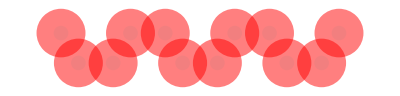
HubbardMeanField initial spin density: -Graphics-

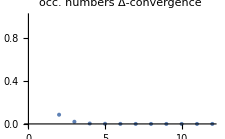
HubbardMeanField SCE convergence: -Graphics-

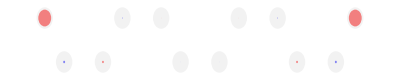
HubbardMeanField final spin density: -Graphics-

{9.74027,Null}

```mathematica
t1=2.7;
U=t1;

np=50;
klist=Table[{0,(2π)/(√(T.T)) i/np,0},{i,0,np-1}];
Temp=4;(* K *)
(* FM *)
spinconfig={
	ConstantArray[0,Length[ruc]],
	ConstantArray[1,Length[ruc]]
}

AbsoluteTiming[{bdup,bddo,μ,occnumbers}=HubbardMeanField[ruc,T,klist,U,t1,"Temperature"->Temp,"SpinDensityScaleFactor"->2,"CMonitor"->True,"SpinConfiguration"->spinconfig];]
```

```mathematica
plotbands[bdup_,bddo_,μ_]:=Show[{ListLinePlot[Most@First@bdup-μ,PlotStyle->Red,GridLines->{None,{0}}],ListLinePlot[Most@First@bddo-μ,PlotStyle->Blue]},PlotRange->3 {-1.0,1.0}];
```

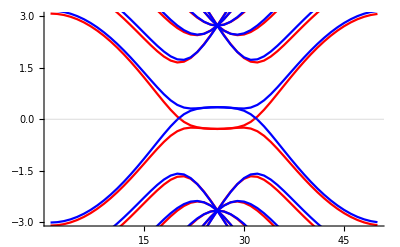

```mathematica
plotbands[bdup,bddo,μ]
```

```mathematica
{bandsup,bandsdo}=First/@{bdup,bddo};
bandsup=Most@bandsup;
bandsdo=Most@bandsdo;
bands=Join[bandsup,bandsdo];
FreeEnergy[Temp,bands,μ]
```

-129.177

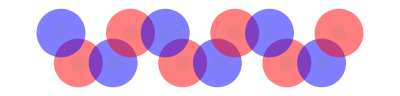
HubbardMeanField initial spin density: -Graphics-

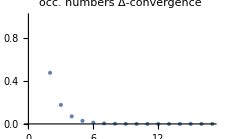
HubbardMeanField SCE convergence: -Graphics-

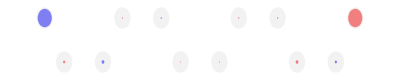
HubbardMeanField final spin density: -Graphics-

{5.27731,Null}

```mathematica
(* AFM configuration *)
spinconfig={
	{0,1,1,0,0,1,1,0,0,1,1,0},{1,0,0,1,1,0,0,1,1,0,0,1}
};

AbsoluteTiming[{bdup,bddo,μ,occnumbers}=HubbardMeanField[ruc,T,klist,U,t1,"Temperature"->Temp,"SpinDensityScaleFactor"->2,"CMonitor"->True,"SpinConfiguration"->spinconfig];]
```

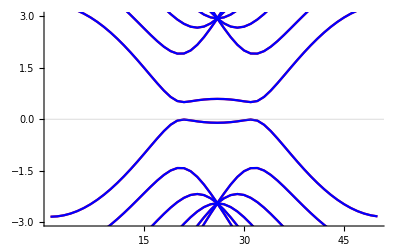

```mathematica
plotbands[bdup,bddo,μ]
```

```mathematica
{bandsup,bandsdo}=First/@{bdup,bddo};
bandsup=Most@bandsup;
bandsdo=Most@bandsdo;
bands=Join[bandsup,bandsdo];
FreeEnergy[Temp,bands,μ]
```

-128.977

It follows from this calculation that FM configuration is more stable than AFM one. This is in contradiction with Magda2014 work...

#### Half-metallic graphene nanoribbons

XXXX Y.-W. Son, M. L. Cohen, and S. G. Louie, Nature 444, 347 (2006).

#### Triangulene

Based on paper S. Mishra et al., Angew. Chemie Int. Ed. 59, 12041 (2020).

```mathematica
data={uc,T,a0}=IVGroupQuantumDot[3,1];
AtomicStructure[data,PlaneProjection->{1,1,0},AtomEnumeration->True]
```

```mathematica
U=3.5;
t1=2.7; (* supplementary materials of S.Mishra et al.,Angew. Chemie Int. Ed.59,12041 (2020) and S.Mishra et al.,J. Am. Chem. Soc.141,10621 (2019).*)

Temp=4;(* K *)
(* FM *)
spinconfig={
	ConstantArray[0,Length[uc]],
	ConstantArray[1,Length[uc]]
}
(* AFM *)
(*spinconfig={{1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1}}*)

AbsoluteTiming[{bdup,bddo,μ,occnumbers}=HubbardMeanField[uc,T,{{0,0,0}},U,t1,"Temperature"->Temp,"SpinDensityScaleFactor"->2,"CMonitor"->True,"SpinConfiguration"->spinconfig];]
```

```mathematica
p1=ListLinePlot[{{1,#⟦1⟧-μ},{2,#⟦1⟧-μ}}&/@Most[bdup⟦1⟧],PlotRange->{{0.9,2.1},1.7{-2,2}},PlotStyle->Directive[{Opacity[0.4],Red,AbsoluteThickness[2]}],Ticks->{None,Automatic},Axes->{False,True}(*GridLines->{None,{μ}}*)];
p2=ListLinePlot[{{1,#⟦1⟧-μ},{2,#⟦1⟧-μ}}&/@Most[bddo⟦1⟧],PlotStyle->Directive[{Opacity[0.2],Blue,AbsoluteThickness[3]}]];
Show[{p1,p2},AspectRatio->2,ImageSize->{300}]
```

These results are in agreement with Fig. 3 (b) of S. Mishra et al., Angew. Chemie Int. Ed. 59, 12041 (2020).

#### Extended triangulene

Here we follow S. Mishra et al., J. Am. Chem. Soc. 141, 10621 (2019).

```mathematica
data={uc,T,a0}=IVGroupQuantumDot[4,1];
AtomicStructure[data,PlaneProjection->{1,1,0},AtomEnumeration->True]
```

```mathematica
U=3.5;
t1=2.7; (* supplementary materials of S.Mishra et al.,Angew. Chemie Int. Ed.59,12041 (2020) and S.Mishra et al.,J. Am. Chem. Soc.141,10621 (2019).*)

Temp=4;(* K *)
(* FM *)
spinconfig={
	ConstantArray[0,Length[uc]],
	ConstantArray[1,Length[uc]]
}
(* AFM *)
spinconfig={{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

AbsoluteTiming[{bdup,bddo,μ,occnumbers}=HubbardMeanField[uc,T,{{0,0,0}},U,t1,"Temperature"->Temp,"SpinDensityScaleFactor"->2,"CMonitor"->True,"SpinConfiguration"->spinconfig];]
```

```mathematica
p1=ListLinePlot[{{1,#⟦1⟧-μ},{2,#⟦1⟧-μ}}&/@Most[bdup⟦1⟧],PlotRange->{{0.9,2.1},1.7{-2,2}},PlotStyle->Directive[{Opacity[0.4],Red,AbsoluteThickness[2]}],Ticks->{None,Automatic},Axes->{False,True}(*GridLines->{None,{μ}}*)];
p2=ListLinePlot[{{1,#⟦1⟧-μ},{2,#⟦1⟧-μ}}&/@Most[bddo⟦1⟧],PlotStyle->Directive[{Opacity[0.2],Blue,AbsoluteThickness[3]}]];
Grid[{{"general view","zoom to Ef"},{Show[{p1,p2},AspectRatio->2,ImageSize->{300}],Show[{p1,p2},AspectRatio->2,ImageSize->{300},PlotRange->{-0.1,1}]}}]
```

These energy levels are in agreement with Fig. 2 (b) in S. Mishra et al., J. Am. Chem. Soc. 141, 10621 (2019).

### Summary

Phase diagram t/U vs ne

t-J model?

More About

Xxxx  Y. Claveau, B. Arnaud, and S. Di Matteo, Eur. J. Phys. 35, 035023 (2014).

Related Tutorials

Related Wolfram Education Group Courses